```mathematica
(* IMPORT MODULES *)
ClearAll[m1,m2,m3]
loadDumpSaves=True;
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/parameters.nb"];
NotebookEvaluate["modules/golden_search.nb"];
If[loadDumpSaves,NotebookEvaluate["modules/load_dump_saves.nb"]];
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* For loop for calculating temperature curves *)
temps=Table[t,{t,0,1,0.1}];
dict=<|uq->"u",sq->"s",cq->"c",bq->"b"|>;
save=True;(* Do you want to save the results? *)

tempData={};
For[iter=1,iter≤Length[temps],iter++,
temp=temps[[iter]];
ClearAll[J,P,flavourSym,γMax,Λ,m1,m2,m3,ham,sM,t1,t2];
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
P=1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
flavourSym=0;(* Flavour symmetry 1 = symmetric, 0 = antisymmetric *)
γMax=12;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
S=1/2;(* Total spin *)
m1=uq;(* mass of quark 1 *)
m2=uq;(* mass of quark 2 *)
m3=cq;(* mass of quark 3 *)
excited=4;(* Choose excited state, 0 for ground state *)
temperature=temp;
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)

(* all different masses = 0, two equal masses = 1, all equal masses = 2 *)
case=If[m1==m2,1,0];
case=If[m1==m2==m3,2,case];
states=allStates[J,P,Λ,S,γMax];
sM=stateMatrix[J,P,Λ,S,γMax];

(* Calculate generalised transformation matrices *)
{t1time,t1}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,1]];
(*Print["Time taken to compute t1: ", ToString[t1time]];*)
{t2time,t2}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,2]];
(*Print["Time taken to compute t2: ", ToString[t2time]];*)
DumpSave["modules/dumpSave/summationVariables.mx",summationVariables];
DumpSave["modules/dumpSave/talmi.mx",talmi];

(* Obtain projector matrix *)
proj=projector[states,flavourSym,case];

(* Required matrices for hamiltonian *)
vCoulomb=polynomialOperatorRho[sM,-1];(* 1/ρ matrix dimensionless *)
vLinear=polynomialOperatorRho[sM,1];(* ρ matrix dimensionless *)
qhoSpect=qhoSpectrum[sM];
kineticRho=polynomialOperatorRho[sM,2];
kineticLam=polynomialOperatorLambda[sM,2];
ham[ω_]:=Hb[ω,temperature,m1,m2,m3,proj];

(* Find minimum and errors*)
{minTime,{a,b,data}}=AbsoluteTiming[goldenSearch[ham,excited+1,0.01,0.9,0.05]];
(*Print["Time taken to find minimum: ", ToString[minTime]];*)
wMin=(a+b)/2;
hamiltonian=ham[wMin];
eigvalMin=Eigenvalues[hamiltonian][[-excited-1]];
AppendTo[tempData,{temp,eigvalMin}];
Print[iter,". t = ", temp,", ω = ",wMin, ", E = ",eigvalMin];
(*Print["{ω_min, E_min}: ",{Around[wMin,a-wMin],eigvalMin}];
Print["Number of basis functions (matrix size): ", Length[hamiltonian]];*)
(* Dump Saves *)

DumpSave["modules/dumpSave/nineJ.mx",nineJ];
DumpSave["modules/dumpSave/rel.mx",rel];
DumpSave["modules/dumpSave/Rcoeff.mx",Rcoeff];
DumpSave["modules/dumpSave/Lcoeff.mx",Lcoeff];
]

If[save&&NumberQ[tempData[[1,2]]],
temperatureData[J_,P_,flavourSym_,γMax_,Λ_,S_,m1_,m2_,m3_,excited_,tempData_]:=temperatureData[J,P,flavourSym,γMax,Λ,S,m1,m2,m3,excited]=tempData;
temperatureData[J,P,flavourSym,γMax,Λ,S,m1,m2,m3,excited,tempData];
DumpSave["modules/dumpSave/temperature_data.mx",temperatureData];
Print["Saved temperature data successfully"],
Print["Data not saved"]
];
```

1. t = 0., ω = 0.355804, E = 3.32007

2. t = 0.1, ω = 0.355804, E = 3.31266

3. t = 0.2, ω = 0.355804, E = 3.29018

4. t = 0.3, ω = 0.355804, E = 3.25169

5. t = 0.4, ω = 0.355804, E = 3.1955

6. t = 0.5, ω = 0.325151, E = 3.11848

7. t = 0.6, ω = 0.325151, E = 3.01554

8. t = 0.7, ω = 0.294498, E = 2.87777

9. t = 0.8, ω = 0.275553, E = 2.68635

10. t = 0.9, ω = 0.214246, E = 2.38999

11. t = 1., ω = 0.034799, E = 1.21853

Saved temperature data successfully

```mathematica
tempData
```

{{0.,3.34753},{0.1,3.34016},{0.2,3.31779},{0.3,3.27901},{0.4,3.22213},{0.5,3.1447},{0.6,3.04115},{0.7,2.90295},{0.8,2.71031},{0.9,2.41041},{1.,1.23318}}

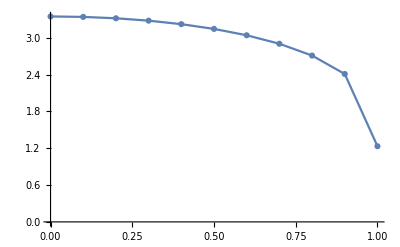

```mathematica
ListPlot[tempData,Joined->True,PlotMarkers->Automatic]
```

```mathematica
?temperatureData
```

```mathematica
m1=sq;
m2=sq;
m3=cq;
fs=1;
pos=temperatureData[1/2,+1,fs,8,0,1/2,m1,m2,m3,0];
neg=temperatureData[1/2,-1,fs,8,1,1/2,m1,m2,m3,0];
pos1=temperatureData[1/2,+1,0,8,0,1/2,uq,uq,cq,1];
imgSize=420;
imagePadding={{90,10},{45,10}};

SetOptions[ListPlot,
Frame->True,
Joined->True,
Axes->True,
FrameLabel->{"T/T_c","E [GeV]"},
PlotMarkers->{Automatic,Automatic,False,False,False},
ImagePadding->imagePadding,
ImageSize->imgSize,
PlotStyle->{Lighter[Blue],Lighter[Red],{Lighter[Black],Dashed},{Lighter[Blue],Dashed,Thin},{Lighter[Red],Dashed,Thin}},
LabelStyle->{FontFamily->"Arial",FontSize->14}];

plotLabels={pos[[-1,2]],neg[[-1,2]],m1+m2+m3-1/2(3Cqqq)};
plotPositions={{1.0005,pos[[-1,2]]},{1.0005,neg[[-1,2]]},{1.0005,m1+m2+m3-1/2(3Cqqq)}};
E0=m1+m2+m3-1/2(3Cqqq);
dashedLine=Table[{t,E0},{t,0,1,0.1}];
dashedPos=Table[{t,pos[[1,2]]},{t,0,1,0.1}];
dashedNeg=Table[{t,neg[[1,2]]},{t,0,1,0.1}]

main=ListPlot[{pos,neg,dashedLine,dashedPos,dashedNeg},
PlotLabel->"ssc Ω_c, J=1/2",
PlotLegends->Placed[{"P=+1","P=-1","E_0"},{Right,Top}],
PlotRange->{Automatic,{1.5,4.5}}
];

sub=ListPlot[{pos,neg,dashedLine,dashedPos},
PlotRange->{{0.99,1.01},{E0-0.062,E0+0.005}},
PlotLabels->Placed[plotLabels,plotPositions],
PlotLabel->"T=T_c (zoom). ssc Ω_c, J=1/2",
PlotLegends->Placed[{"P=+1","P=-1","E_0"},{Left,Bottom}]
];

grid=Grid[{{main,sub}}]
```

{{0.,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.1,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.2,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.3,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.4,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.5,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.6,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.7,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.8,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.9,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{1.,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧}}

ListPlot[{temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0],temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0],{{0.,1.74185},{0.1,1.74185},{0.2,1.74185},{0.3,1.74185},{0.4,1.74185},{0.5,1.74185},{0.6,1.74185},{0.7,1.74185},{0.8,1.74185},{0.9,1.74185},{1.,1.74185}},{{0.,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.1,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.2,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.3,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.4,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.5,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.6,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.7,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.8,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.9,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{1.,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧}},{{0.,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.1,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.2,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.3,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.4,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.5,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.6,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.7,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.8,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.9,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{1.,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦1,2⟧}}},PlotLabel→ssc Ω_c, J=1/2,PlotLegends→Placed[{P=+1,P=-1,E_0},{Right,Top}],PlotRange→{Automatic,{1.5,4.5}}] | ListPlot[{temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0],temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0],{{0.,1.74185},{0.1,1.74185},{0.2,1.74185},{0.3,1.74185},{0.4,1.74185},{0.5,1.74185},{0.6,1.74185},{0.7,1.74185},{0.8,1.74185},{0.9,1.74185},{1.,1.74185}},{{0.,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.1,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.2,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.3,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.4,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.5,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.6,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.7,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.8,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{0.9,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧},{1.,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦1,2⟧}}},PlotRange→{{0.99,1.01},{1.67985,1.74685}},PlotLabels→Placed[{temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦-1,2⟧,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦-1,2⟧,1.74185},{{1.0005,temperatureData[1/2,1,1,8,0,1/2,0.577,0.577,1.836,0]⟦-1,2⟧},{1.0005,temperatureData[1/2,-1,1,8,1,1/2,0.577,0.577,1.836,0]⟦-1,2⟧},{1.0005,1.74185}}],PlotLabel→T=T_c (zoom). ssc Ω_c, J=1/2,PlotLegends→Placed[{P=+1,P=-1,E_0},{Left,Bottom}]]

```mathematica
Export["plots/ch8_ssc_jhalf_pVSn.pdf",grid,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch8_ssc_jhalf_pVSn.pdf

{{0.,3.00393},{0.1,3.00393},{0.2,3.00393},{0.3,3.00393},{0.4,3.00393},{0.5,3.00393},{0.6,3.00393},{0.7,3.00393},{0.8,3.00393},{0.9,3.00393},{1.,3.00393}}

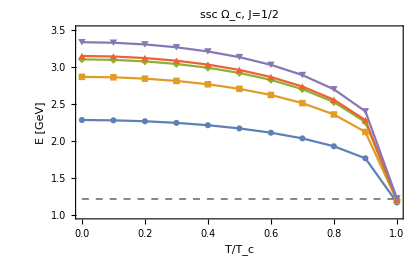
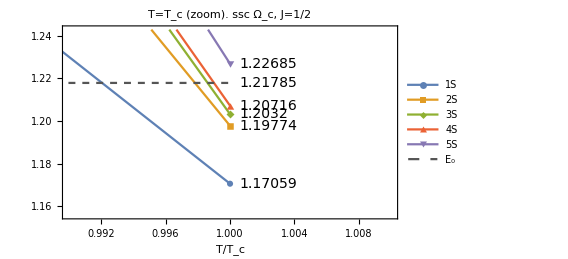
-Graphics- | -Graphics-

```mathematica
m1=uq;
m2=uq;
m3=cq;
fs=0;
pos1=temperatureData[1/2,+1,fs,8,0,1/2,m1,m2,m3,0];
pos2=temperatureData[1/2,+1,fs,8,0,1/2,m1,m2,m3,1];
pos3=temperatureData[1/2,+1,fs,8,0,1/2,uq,uq,cq,2];
pos4=temperatureData[1/2,+1,fs,8,0,1/2,uq,uq,cq,3];
pos5=temperatureData[1/2,+1,fs,10,0,1/2,uq,uq,cq,4];
imgSize=420;
imagePadding={{50,10},{45,10}};

SetOptions[ListPlot,
Frame->True,
Joined->True,
Axes->True,
FrameLabel->{"T/T_c","E [GeV]"},
PlotMarkers->{Automatic,Automatic,Automatic,Automatic,Automatic,False},
ImagePadding->imagePadding,
ImageSize->imgSize,
PlotStyle->{{Automatic},{Automatic},{Automatic},{Automatic},{Automatic},{Lighter[Black],Dashed,Thin}},
LabelStyle->{FontFamily->"Arial",FontSize->14}];

plotLabels={pos1[[-1,2]],pos2[[-1,2]],pos3[[-1,2]],pos4[[-1,2]],pos5[[-1,2]],m1+m2+m3-1/2(3Cqqq)};
plotPositions={{1.0005,pos1[[-1,2]]},{1.0005,pos2[[-1,2]]},{1.0005,pos3[[-1,2]]},{1.0005,pos4[[-1,2]]},{1.0005,pos5[[-1,2]]},{1.0005,m1+m2+m3-1/2(3Cqqq)}};
E0=m1+m2+m3-1/2(3Cqqq);
dashedLine=Table[{t,E0},{t,0,1,0.1}];
dashedPos=Table[{t,pos[[1,2]]},{t,0,1,0.1}];
dashedNeg=Table[{t,neg[[1,2]]},{t,0,1,0.1}]

main=ListPlot[{pos1,pos2,pos3,pos4,pos5,dashedLine},
PlotLabel->"ssc Ω_c, J=1/2",

PlotRange->{Automatic,{1,3.5}}
];

sub=ListPlot[{pos1,pos2,pos3,pos4,pos5,dashedLine},
PlotRange->{{0.99,1.01},{E0-0.062,E0+0.025}},
PlotLabels->Placed[plotLabels,plotPositions],
PlotLegends->Placed[{"1S","2S","3S","4S","5S","E_0"},{After,Top}],
PlotLabel->"T=T_c (zoom). ssc Ω_c, J=1/2",
FrameLabel->{"T/T_c",""}
];

grid=Grid[{{main,sub}}]
```